```mathematica
ψ1[x_]:=Piecewise[{{3.93847*(10^5)*Exp[3.8*(10^9)* x],x<-a},{28136.57Cos[1.2523*(10^9)* x],-a<=x<=a},{3.93847*(10^5)*Exp[-3.8*(10^9)*x],x>a}}];
```

```mathematica
ψ2[x_]:=Piecewise[{{-393630*Exp[3.14*(10^9)* x],x<-a},{27540.05*Sin[2.47458*(10^9)* x],-a<=x<=a},{393630*Exp[-3.14*(10^9)*x],x>a}}];
ψ3[x_]:=Piecewise[{{-1.3048*(10^5)*Exp[1.75*(10^9)* x],x<-a},{25226*Cos[3.5953*(10^9)* x],-a<=x<=a},{-1.3048*(10^5)*Exp[-1.75*(10^9)* x],x>a}}];
```

```mathematica
a = 1 * (10^(-9))
```

1/1000000000

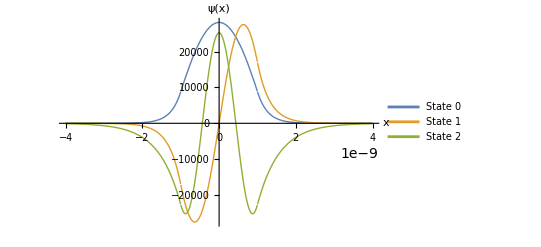

```mathematica
Plot[{ψ1[x],ψ2[x],ψ3[x]},{x,-4 a,4 a},PlotRange->All,PlotLegends->{"State 0","State 1","State 2"},AxesLabel->{"x","ψ(x)"},PlotStyle->Thick]
```

```mathematica
Export["/home/joejoe/texhw/PEP 553/FinitePotentialWell /wavefunctions.pdf",%7,"PDF"]
```

/home/joejoe/texhw/PEP 553/FinitePotentialWell /wavefunctions.pdf